```mathematica
5898765100:{"AA"->"B","AB"->"BA","B"->"AAA"}
```

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
5898765100:{"AA"->"B","AB"->"BA","B"->"AAA"}
```

Syntax::tsntxi: "5898765100:{AA->B,AB->BA,B->AAA}" is incomplete; more input is needed.

```mathematica
rs01=FromReducedRankIndex[5898765100]
```

<|Index→5898765100,QCode→32423424324233,RuleSet→{AA→B,AB→BA,B→AAA}|>

```mathematica
rs01[["RuleSet"]]
```

{AA→B,AB→BA,B→AAA}




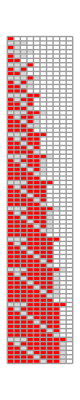
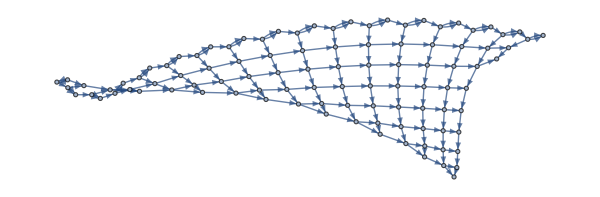
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss01=SSS[rs01[["RuleSet"]], "B",500,
 SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic];
```

```mathematica
sss01[["Net"]]//Short
```

{1→2,1→2,2→3,3→4,3→4,3→5,1→5,«945»,497→498,476→498,498→499,477→499,499→500,478→500}

```mathematica
nds01=ToNetDifferenceSets[sss01[["Net"]]]
```

{{1,1,4},{1},{1,1,2},{2},{3},{1,1,2},{2},{3,4},{1,1,2},{3},{1,4},{4},{1,1,2},{3},{1,4},{4,5},{1,1,2},{4},{1,5},{1,5},{5},{1,1,2},{4},{1,5},{1,5},{5,6},{1,1,2},{5},{1,6},{1,6},{1,6},{6},{1,1,2},{5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{6},{1,7},{1,7},{1,7},{1,7},{7},{1,1,2},{6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{7},{1,8},{1,8},{1,8},{1,8},{1,8},{8},{1,1,2},{7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9},{1,1,2},{8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10},{1,1,2},{9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11},{1,1,2},{10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12},{1,1,2},{11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13},{1,1,2},{12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14},{1,1,2},{13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15},{1,1,2},{14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16},{1,1,2},{15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,1,2},{16},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17},{1,1,2},{16},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17,18},{1,1,2},{17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18},{1,1,2},{17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,1,2},{18},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19},{1,1,2},{18},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19,20},{1,1,2},{19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20},{1,1,2},{19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,1,2},{20},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21},{1,1,2},{20},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21,22},{1,1,2},{21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1},{},{1,1,2},{},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
rslo1=ReduceSetList[nds01]
```

{{1,1,4},{1},{1,1,2},€_(n$1⊨1)^2[{1+n$1}],€_(n$2⊨1)^18[{1,1,2},{1+n$2},€^(-1+n$2)[{1,2+n$2}],{2+n$2,3+n$2},{1,1,2},{2+n$2},€^n$2[{1,3+n$2}],{3+n$2}],{1,1,2},{20},€^18[{1,21}],{21,22},{1,1,2},{21},€^18[{1,22}],{1},{},{1,1,2},{},€^17[{1}]}